```mathematica
ELossTableAg = {{1.00,1.290},{1.50,1.331},{2.00,1.387},{2.50,1.446},{3.00,1.506},{3.50,1.566},{4.00,1.624},{4.50,1.683},{5.00,1.741},{6.00,1.854},{6.5,1.910},{7.00,1.967},{7.50,2.022},{8.00,2.077},{8.50,2.133}};
ELossTableAu = {{1.00,2.179},{1.50,2.289},{2.00,2.422},{2.50,2.561},{3.00,2.702},{3.50,2.841},{4.00,2.980},{4.50,3.117},{5.00,3.254},{6.00,3.526},{6.5,3.661},{7.00,3.796},{7.50,3.929},{8.00,4.065},{8.50,4.200}};
```

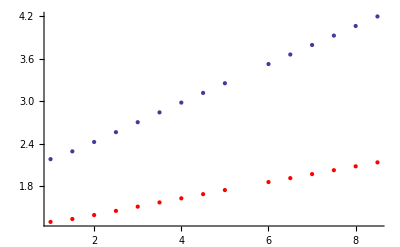

```mathematica
Show[ListPlot[ELossTableAg,PlotStyle->Red],ListPlot[ELossTableAu]]
```

```mathematica
ELossAg = Fit[ELossTableAg,{1,x},x]
ELossAu = Fit[ELossTableAu,{1,x},x]
```

1.16539+0.114273 x

1.88824+0.272318 x

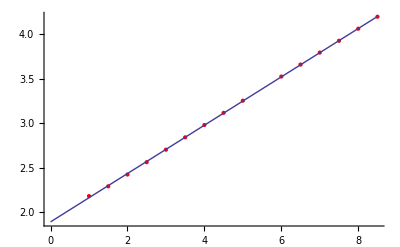

```mathematica
Show[ListPlot[ELossTableAu, PlotStyle->Red],Plot[ELossAu,{x,0,8.5}]]
```

```mathematica
1.888240916271722+0.27231753554502364 5 +1.888240916271722+0.27231753554502364 4.5
```

```mathematica
6.363498420221168/2
```

```mathematica
1/(2*3.181749210110584)
```

0.157146